```mathematica
γ=2.6;α=0.4;ρ=0.63;
```

0.19845 (1.4-3 v)+(1-v) (-0.4+v) v

{v→0.255456}

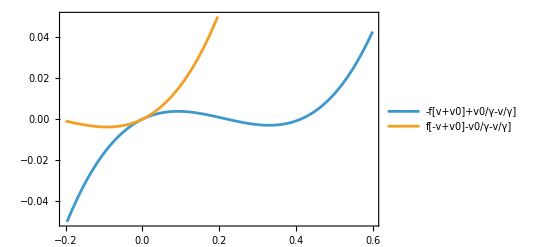

```mathematica
f[v_]=v(1-v)(v-α);
f1[v_]=f[v]+(1+α-3v)ρ^2/2
eqn=FindRoot[f1[v]-v/γ==0,{v,0.2}]
v0=v/.eqn;
Plot[{-f1[v+v0]+v0/γ-v/γ,f1[-v+v0]-v0/γ-v/γ},{v,-0.2,0.6},PlotRange->{-0.05,0.05},Frame->True,PlotLegends->{"-f[v+v0]+v0/γ-v/γ]","f[-v+v0]-v0/γ-v/γ]"}]
```

InterpolatingFunction[…]

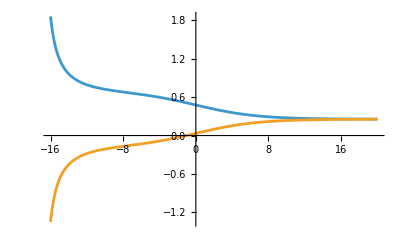

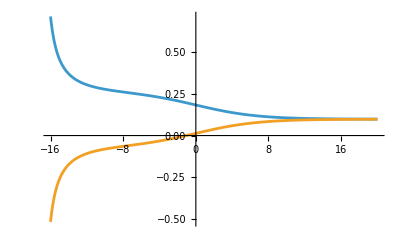

```mathematica
eqn1=FindRoot[-f1[v+v0]+v0/γ-v/γ,{v,0.2}];
eqn2=FindRoot[-f1[v+v0]+v0/γ-v/γ,{v,0.4}];
a=v/.eqn1;
b=v/.eqn2;
V=NDSolveValue[{v''[t]==-f1[v[t]+v0]+v0/γ-v[t]/γ,v[0]==a,v'[0]==-Sqrt[2]Sqrt[Integrate[-f1[u+v0]+v0/γ-u/γ,{u,0,a}]]},v,{t,-16,20}]
Plot[{v0+V[t],v0-V[t]},{t,-16,20}]
Plot[{(v0+V[t])/γ,(v0-V[t])/γ},{t,-16,20}]
```